# Supplementary tensors

## ITensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ITensor`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.039934,Null}

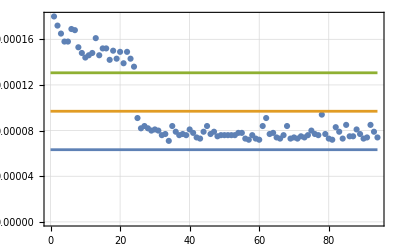

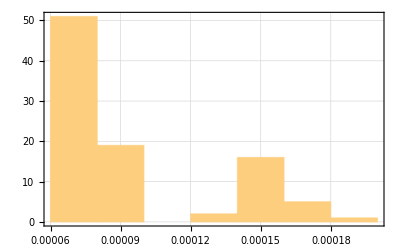

{0.0000632571,0.0000969468,0.000130637}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[2]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.049593,Null}

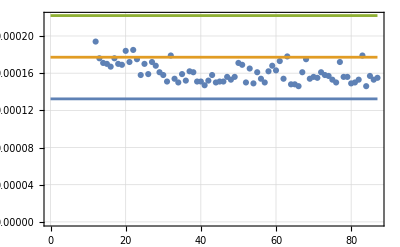

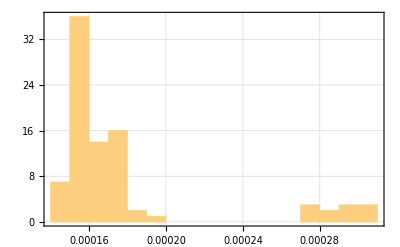

{0.000132348,0.000177149,0.000221951}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[3]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.092846,Null}

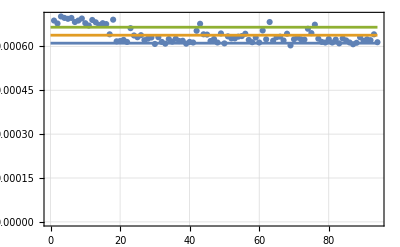

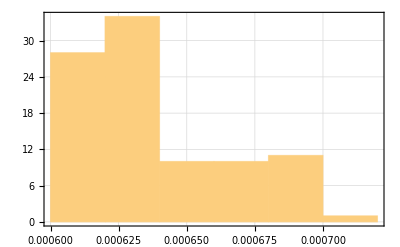

{0.000610687,0.000637957,0.000665228}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[4]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.625318,Null}

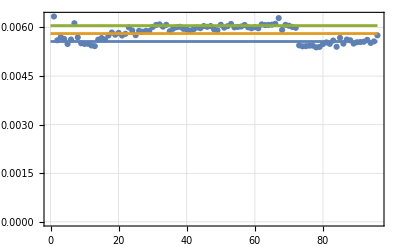

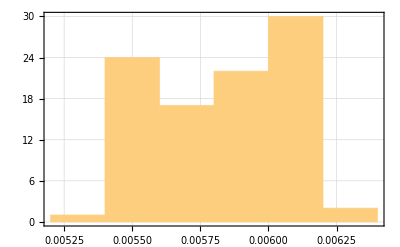

{0.0055673,0.00581272,0.00605813}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[5]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{7.30749,Null}

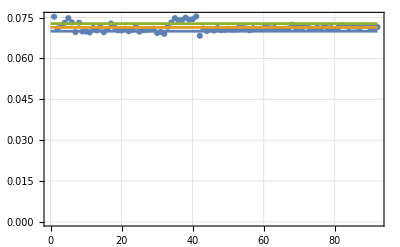

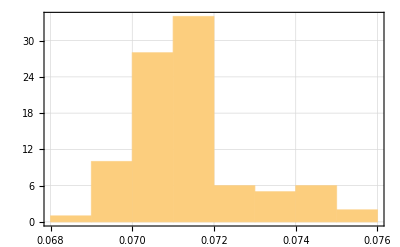

{0.0699803,0.071376,0.0727716}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[6]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CTensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.065448,Null}

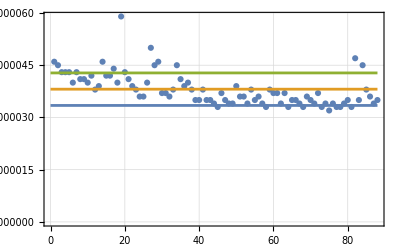

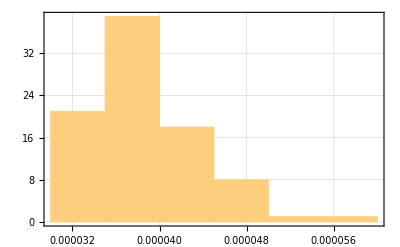

{0.0000334443,0.0000381136,0.000042783}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.075819,Null}

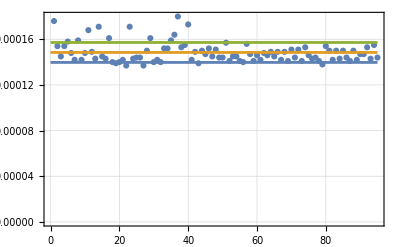

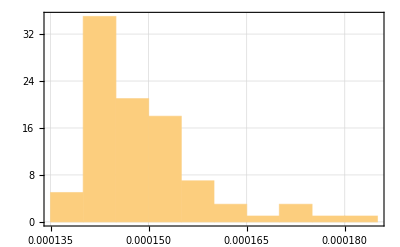

{0.000139726,0.000148463,0.0001572}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.166239,Null}

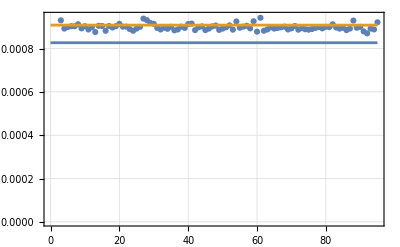

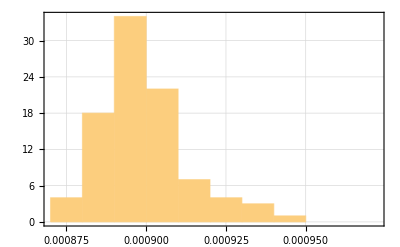

{0.000826757,0.000908063,0.00098937}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.06563,Null}

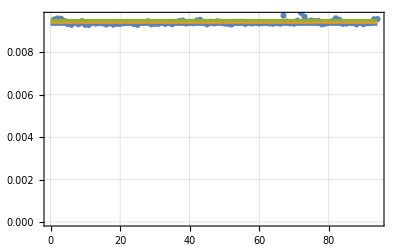

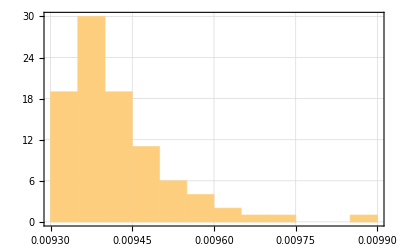

{0.00932165,0.00942013,0.0095186}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{16.4825,Null}

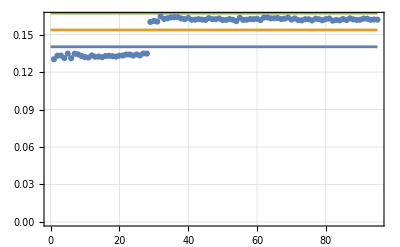

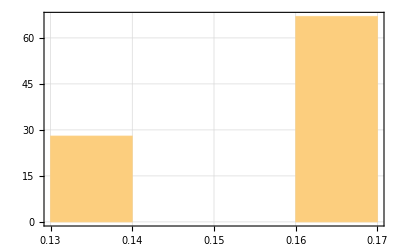

{0.140246,0.153722,0.167199}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{269.125,Null}

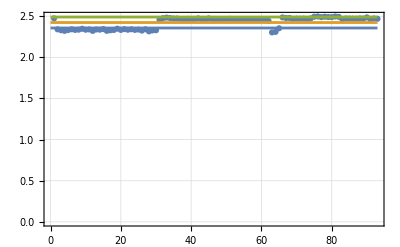

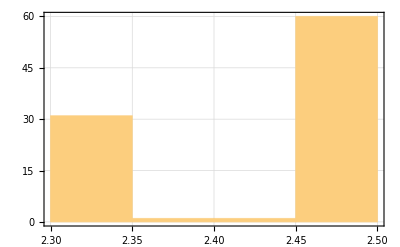

{2.35609,2.42272,2.48934}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C1Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.095467,Null}

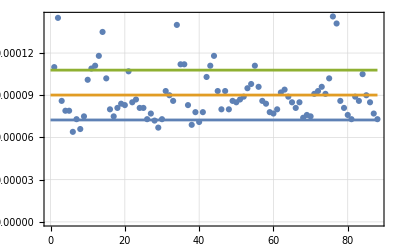

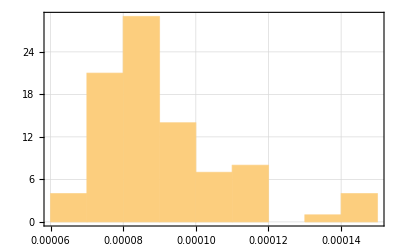

{0.0000724371,0.0000901477,0.000107858}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.094668,Null}

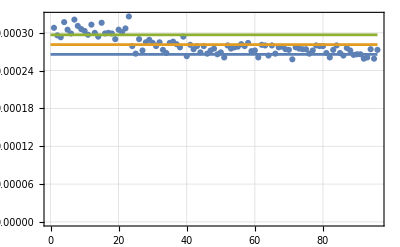

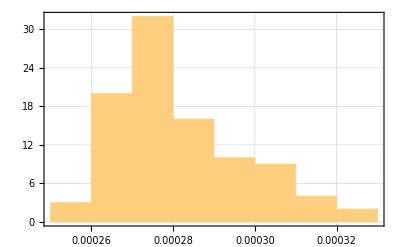

{0.000265822,0.000281333,0.000296845}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.278244,Null}

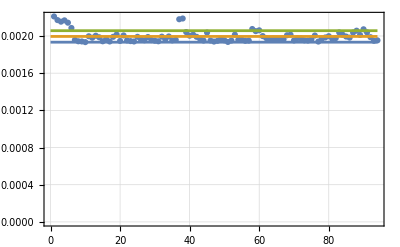

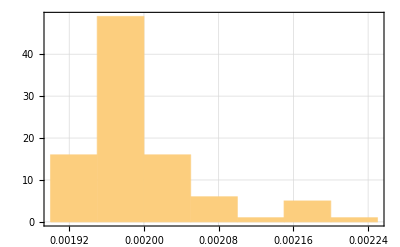

{0.00193323,0.0019951,0.00205696}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{2.41615,Null}

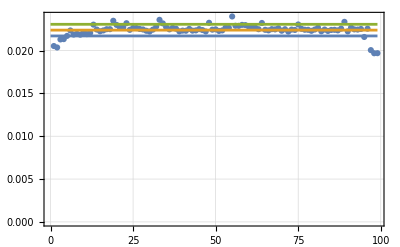

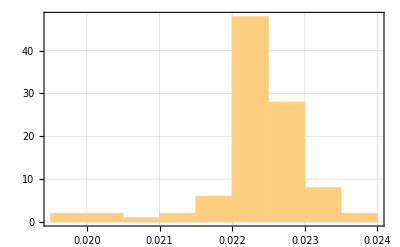

{0.0217062,0.0223852,0.0230643}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{32.5613,Null}

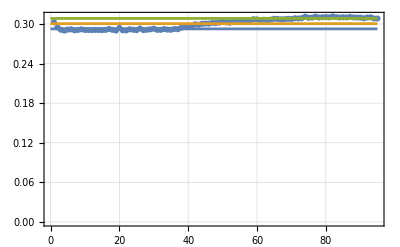

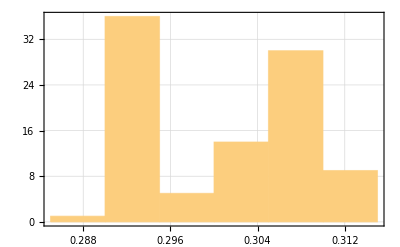

{0.292527,0.300451,0.308374}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{587.821,Null}

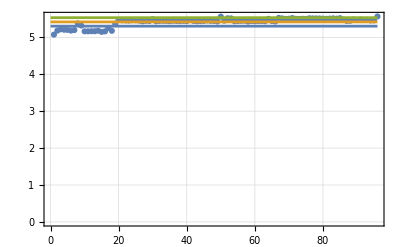

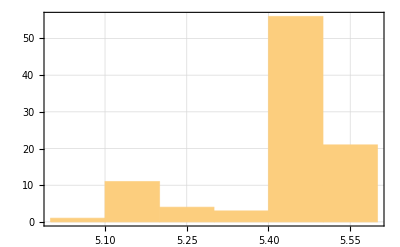

{5.30267,5.4175,5.53232}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C2Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.072682,Null}

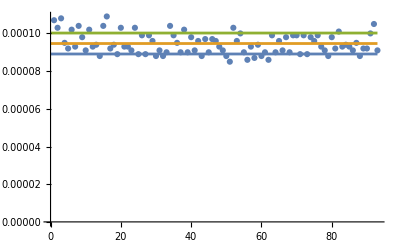

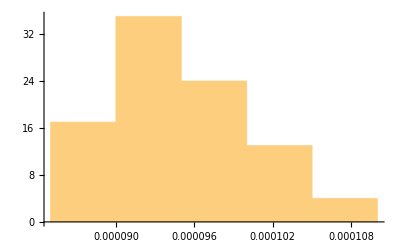

{0.0000890859,0.0000946452,0.000100204}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.116559,Null}

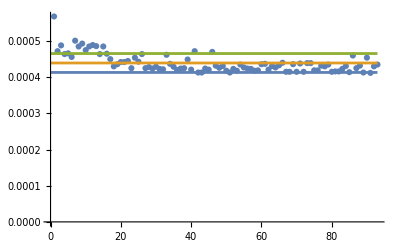

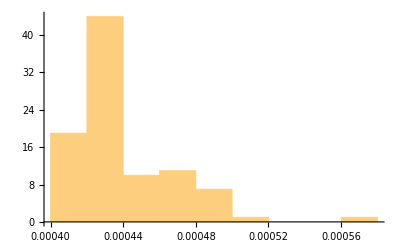

{0.000413198,0.000439344,0.00046549}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.419777,Null}

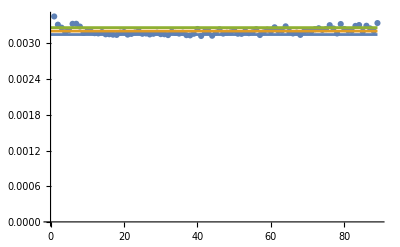

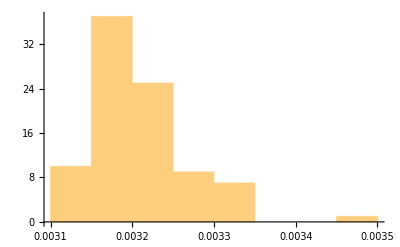

{0.00314898,0.00320727,0.00326556}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{3.82362,Null}

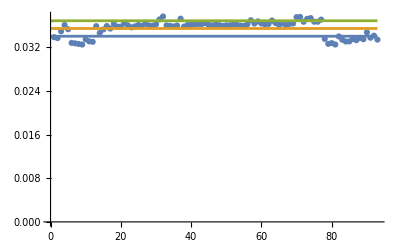

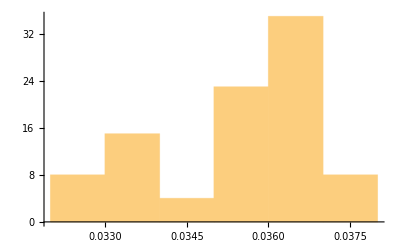

{0.0339959,0.035413,0.0368301}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{53.4165,Null}

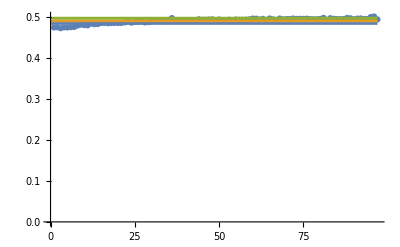

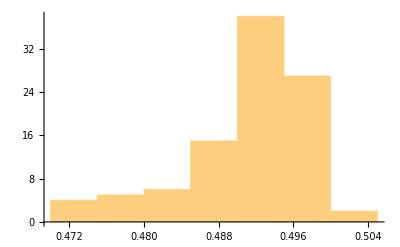

{0.484428,0.490885,0.497342}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{931.357,Null}

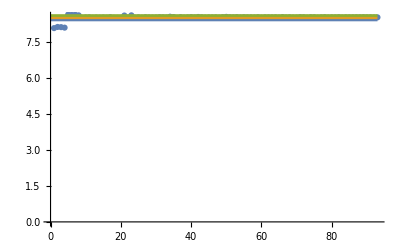

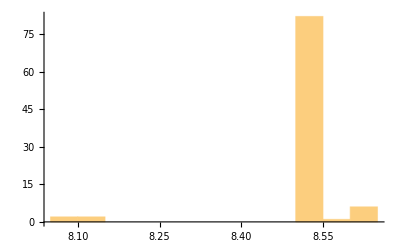

{8.42178,8.51227,8.60276}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C3Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.075487,Null}

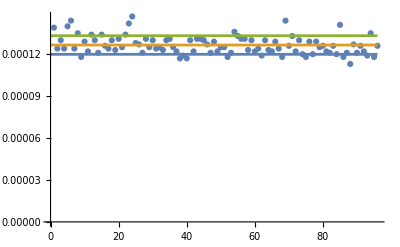

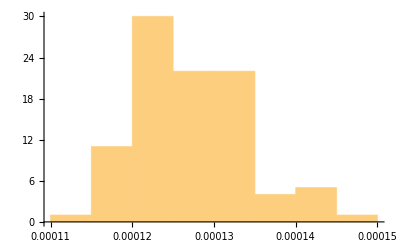

{0.000119911,0.000126563,0.000133214}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.132695,Null}

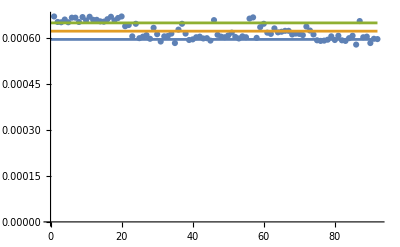

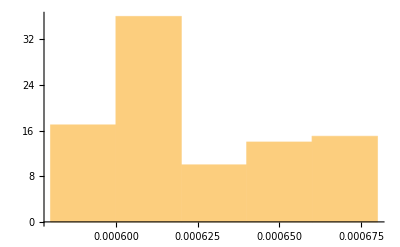

{0.000596902,0.000623913,0.000650924}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.599867,Null}

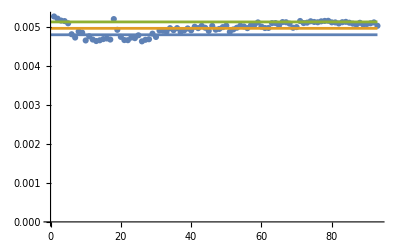

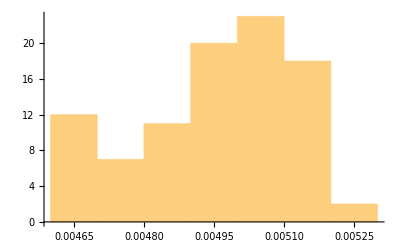

{0.00478841,0.00495283,0.00511724}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{5.20108,Null}

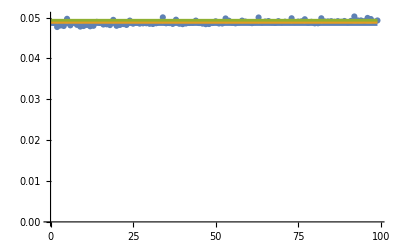

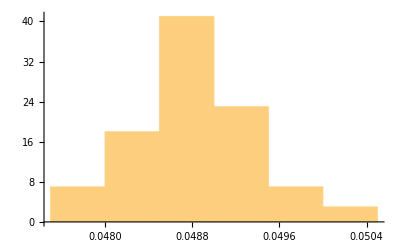

{0.0482832,0.0488067,0.0493302}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{78.0551,Null}

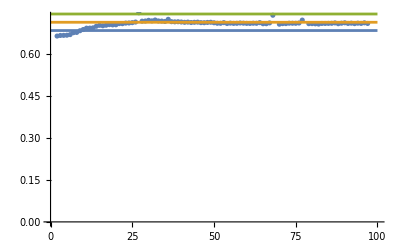

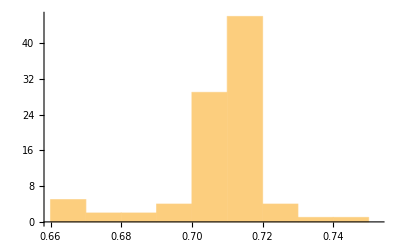

{0.684338,0.713884,0.74343}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1309.13,Null}

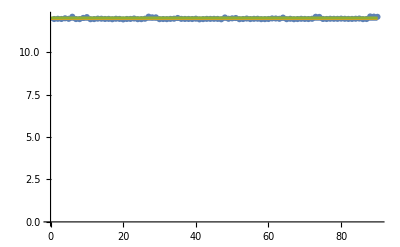

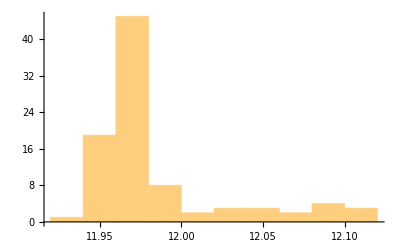

{11.9427,11.9846,12.0264}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C4Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.093308,Null}

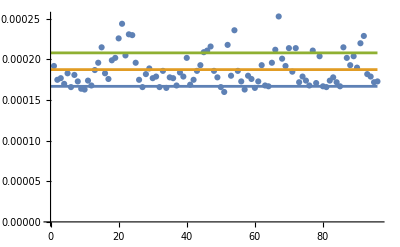

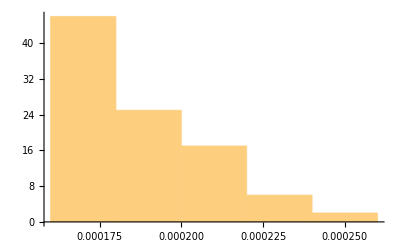

{0.00016695,0.000187552,0.000208155}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.149448,Null}

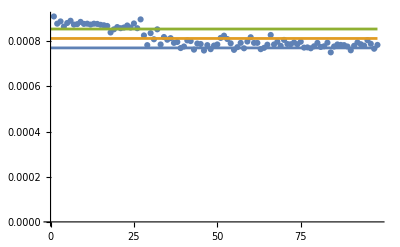

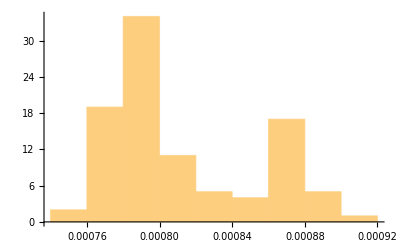

{0.000770692,0.000812531,0.000854369}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.733757,Null}

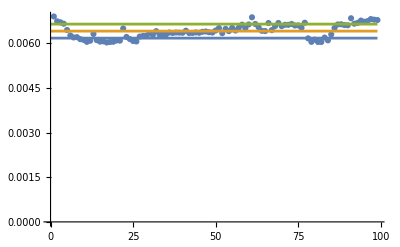

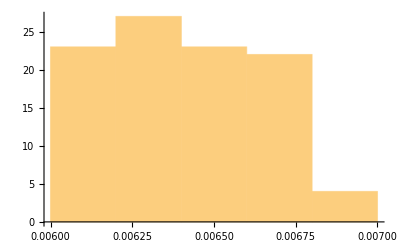

{0.00616767,0.00640308,0.00663849}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{7.24115,Null}

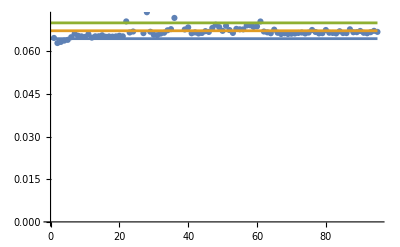

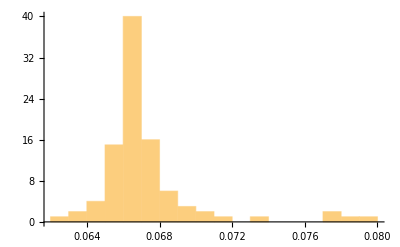

{0.0644244,0.0671978,0.0699712}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{107.232,Null}

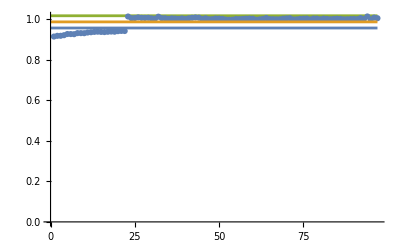

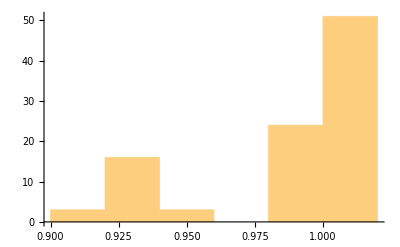

{0.955565,0.985723,1.01588}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1709.49,Null}

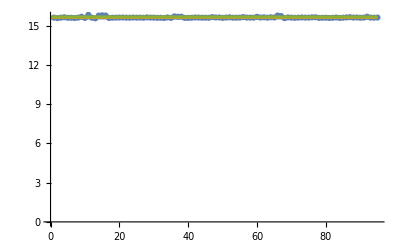

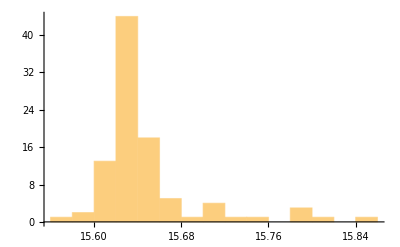

{15.5997,15.647,15.6944}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## ETensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ETensor`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.062487,Null}

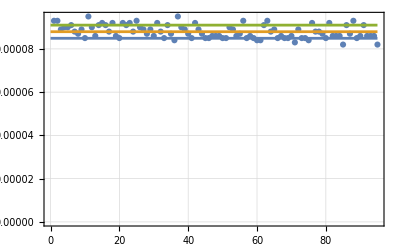

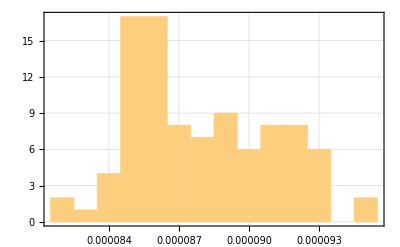

{0.0000849038,0.0000879474,0.0000909909}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ETensor`;
	AppendTo[theData,Timing[ETensor[{μ,𝓂},DummyArray[2]]][[1]]];
	Clear[ETensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.10231,Null}

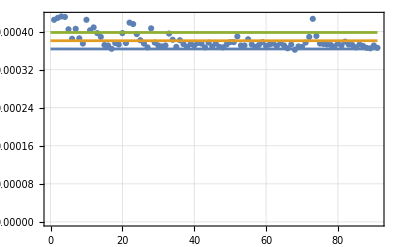

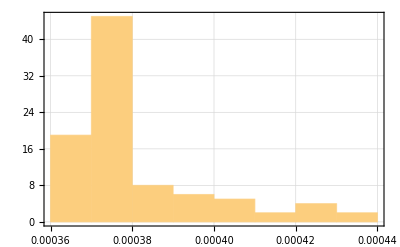

{0.000363647,0.000380967,0.000398287}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ETensor`;
	AppendTo[theData,Timing[ETensor[{μ,𝓂},DummyArray[3]]][[1]]];
	Clear[ETensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.459127,Null}

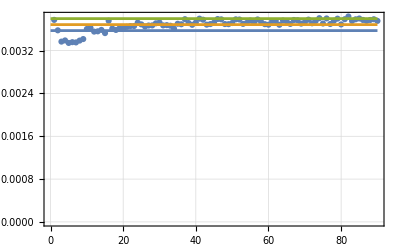

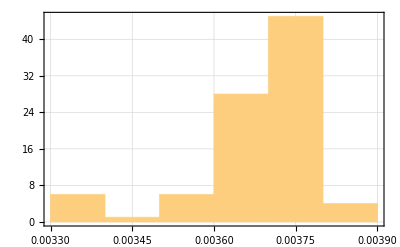

{0.00357474,0.00368667,0.00379859}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ETensor`;
	AppendTo[theData,Timing[ETensor[{μ,𝓂},DummyArray[4]]][[1]]];
	Clear[ETensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{5.86449,Null}

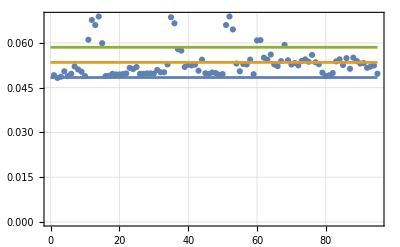

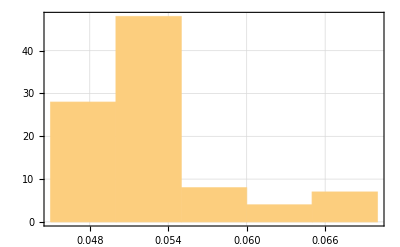

{0.048417,0.0534856,0.0585543}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ETensor`;
	AppendTo[theData,Timing[ETensor[{μ,𝓂},DummyArray[5]]][[1]]];
	Clear[ETensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{93.6494,Null}

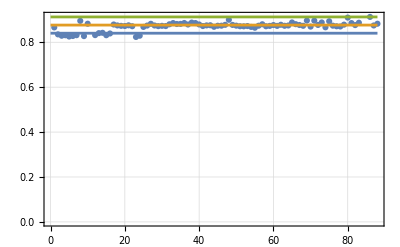

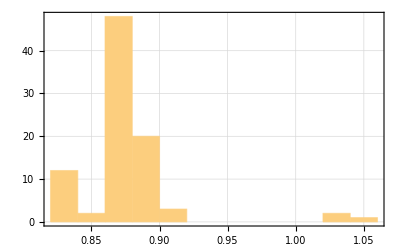

{0.840325,0.876563,0.9128}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ETensor`;
	AppendTo[theData,Timing[ETensor[{μ,𝓂},DummyArray[6]]][[1]]];
	Clear[ETensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CETensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CETensor`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.075665,Null}

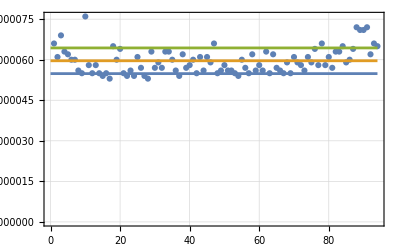

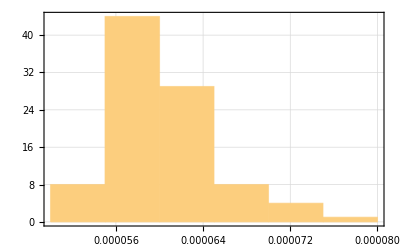

{0.000054854,0.0000596064,0.0000643588}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CETensor`;
	AppendTo[theData,Timing[CETensor[{μ,𝓂},DummyArray[1]]][[1]]];
	Clear[CETensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.107065,Null}

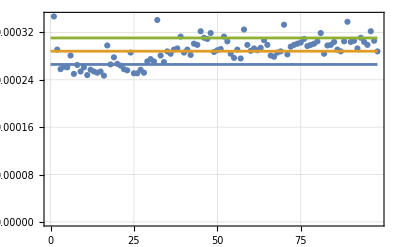

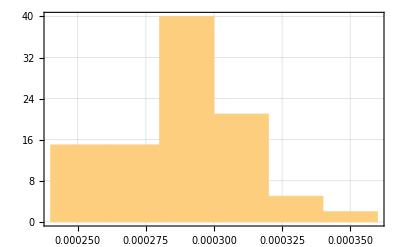

{0.00026593,0.000288306,0.000310682}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CETensor`;
	AppendTo[theData,Timing[CETensor[{μ,𝓂},DummyArray[2]]][[1]]];
	Clear[CETensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.11863,Null}

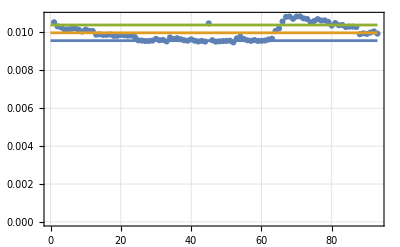

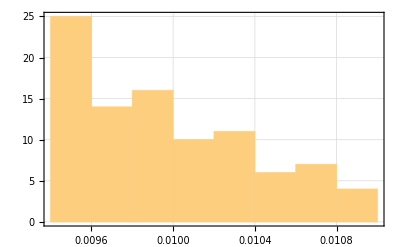

{0.00956929,0.00998224,0.0103952}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CETensor`;
	AppendTo[theData,Timing[CETensor[{μ,𝓂},DummyArray[3]]][[1]]];
	Clear[CETensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{48.4059,Null}

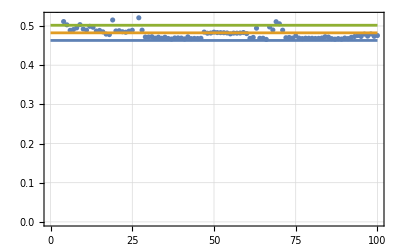

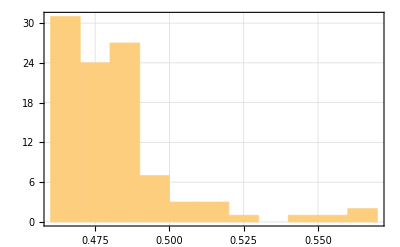

{0.46311,0.482498,0.501885}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CETensor`;
	AppendTo[theData,Timing[CETensor[{μ,𝓂},DummyArray[4]]][[1]]];
	Clear[CETensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

# Scalar-graviton vertices

## Kinetic term

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.57379,Null}

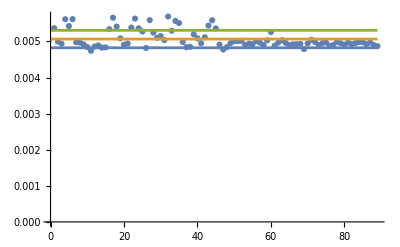

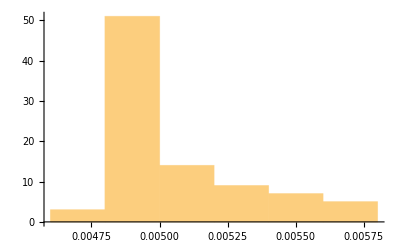

{0.00482536,0.00506712,0.00530889}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[1],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.91979,Null}

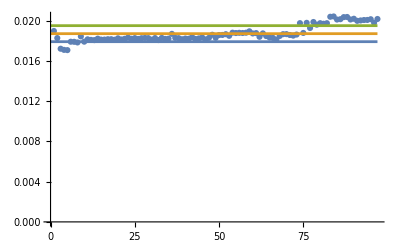

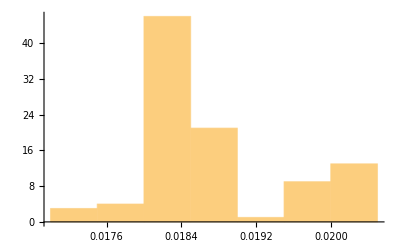

{0.0179016,0.0186976,0.0194936}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[2],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{33.3016,Null}

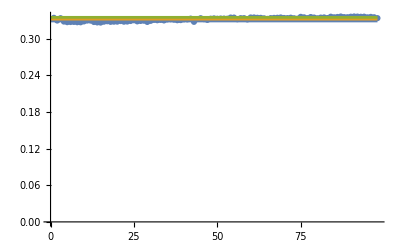

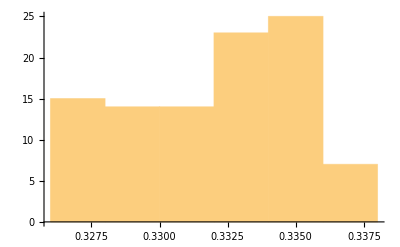

{0.329132,0.332089,0.335047}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[3],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{861.279,Null}

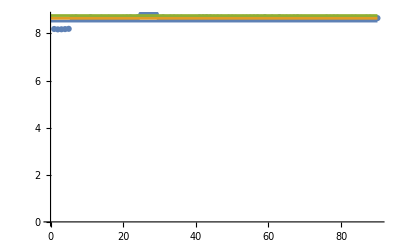

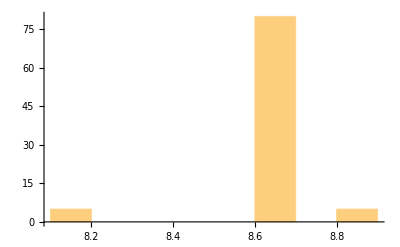

{8.52478,8.64232,8.75987}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[4],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Potential term

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.050793,Null}

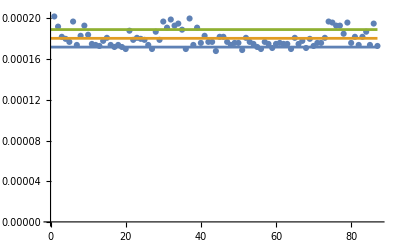

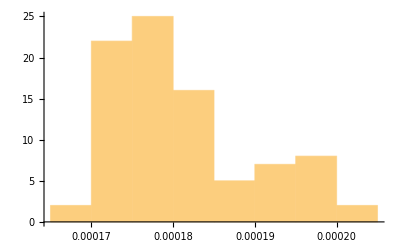

{0.000171879,0.000180494,0.00018911}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[1],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.065125,Null}

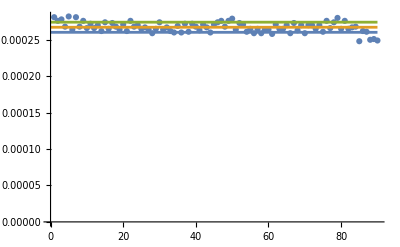

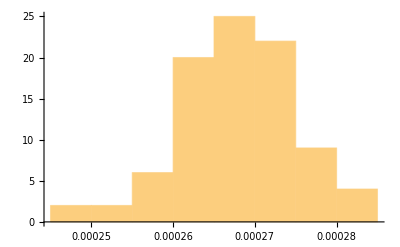

{0.000260232,0.000267189,0.000274146}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[2],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.487913,Null}

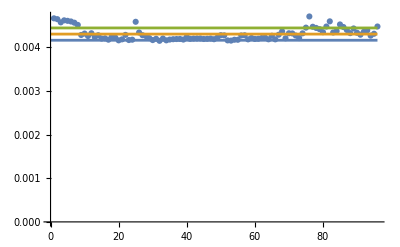

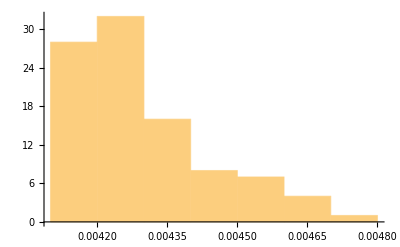

{0.00416113,0.00430204,0.00444296}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[3],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton-fermion vertex

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonFermionVertex`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.354433,Null}

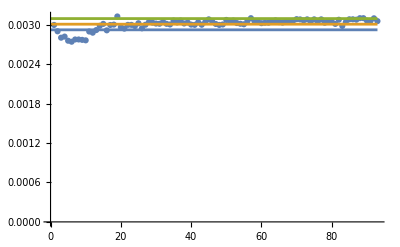

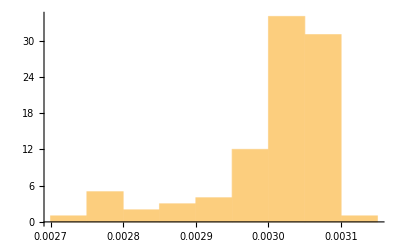

{0.00292078,0.0030063,0.00309182}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[1],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.50745,Null}

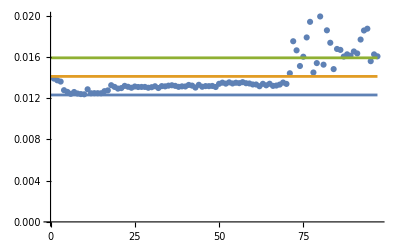

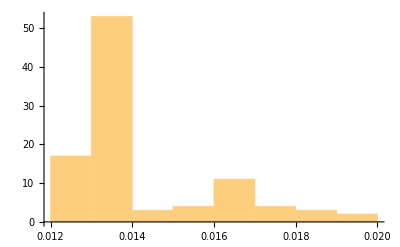

{0.0123104,0.0141116,0.0159127}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[2],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{10.3719,Null}

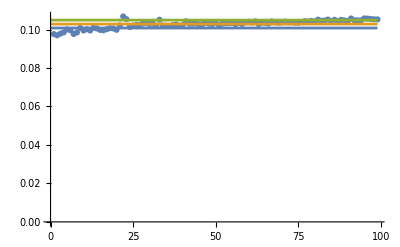

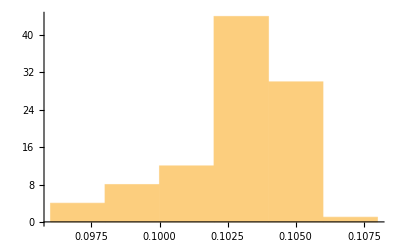

{0.100797,0.102854,0.104912}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[3],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton-vector vertices

## Massive vectors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{3.22913,Null}

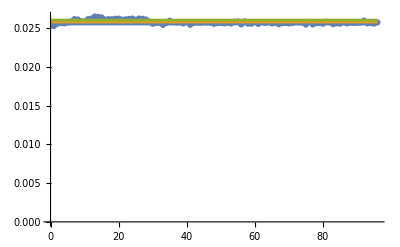

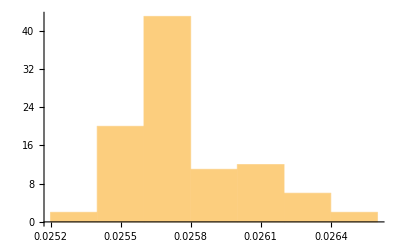

{0.0255203,0.0257732,0.0260262}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[1],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{22.2065,Null}

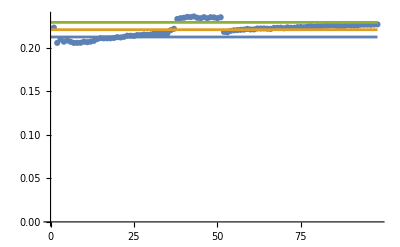

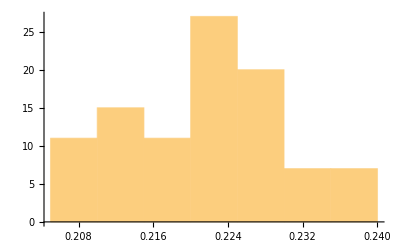

{0.212681,0.221087,0.229493}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[2],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{334.476,Null}

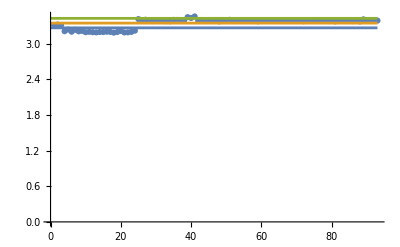

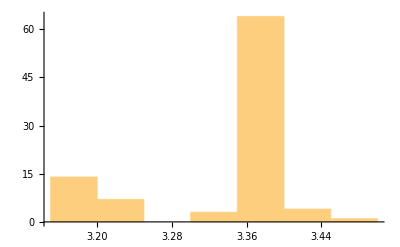

{3.26318,3.34326,3.42333}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[3],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Massless vectors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{4.39894,Null}

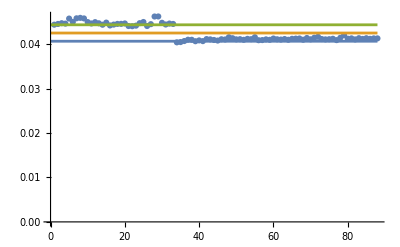

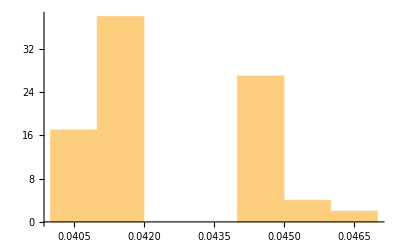

{0.0406498,0.0424975,0.0443453}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[1],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{56.8735,Null}

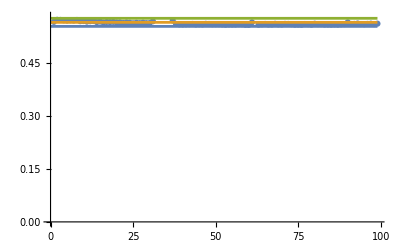

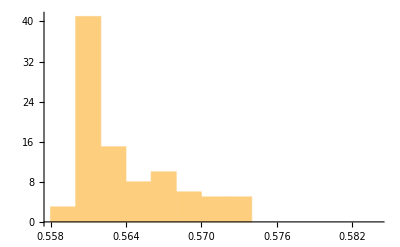

{0.555188,0.566653,0.578118}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[2],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1219.56,Null}

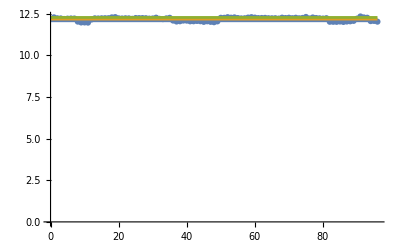

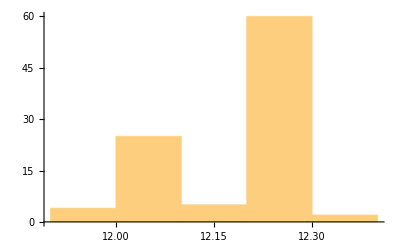

{12.0752,12.1753,12.2753}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[3],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton vertices

## Pure graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
LaunchKernels[];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{11.4381,Null}

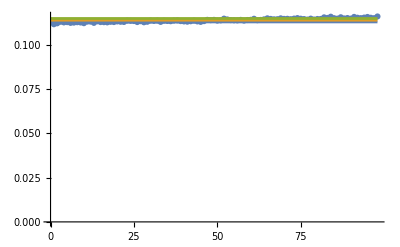

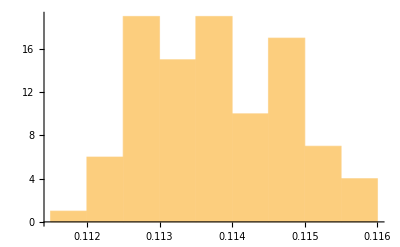

{0.112816,0.113785,0.114753}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonVertex[DummyArrayK[2]]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{487.204,Null}

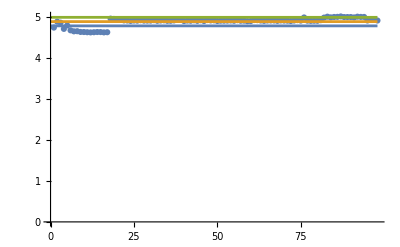

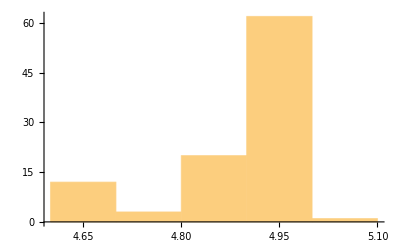

{4.7748,4.87888,4.98296}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonVertex[DummyArrayK[3]]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```